## Constant pressure kappa_ph

```mathematica
fileKappa={"t_kappa_31.ISO.0.01bmf.dat","t_kappa_31.ISO.0.1bmf.dat","t_kappa_31.ISO.1bmf.dat","t_kappa_31.ISO.10bmf.dat","t_kappa_31.ISO.100bmf.dat","t_kappa_31.ISO.BULK.dat","t_kappa_31.PERF.BULK.dat"};

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/noZP_0/"];
kappa0=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/10/"];
kappa10=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/300/"];
kappa300=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/760/"];
kappa760=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/1000/"];
kappa1000=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/1500/"];
kappa1500=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/2500/"];
kappa2500=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/3800/"];
kappa3800=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];
```

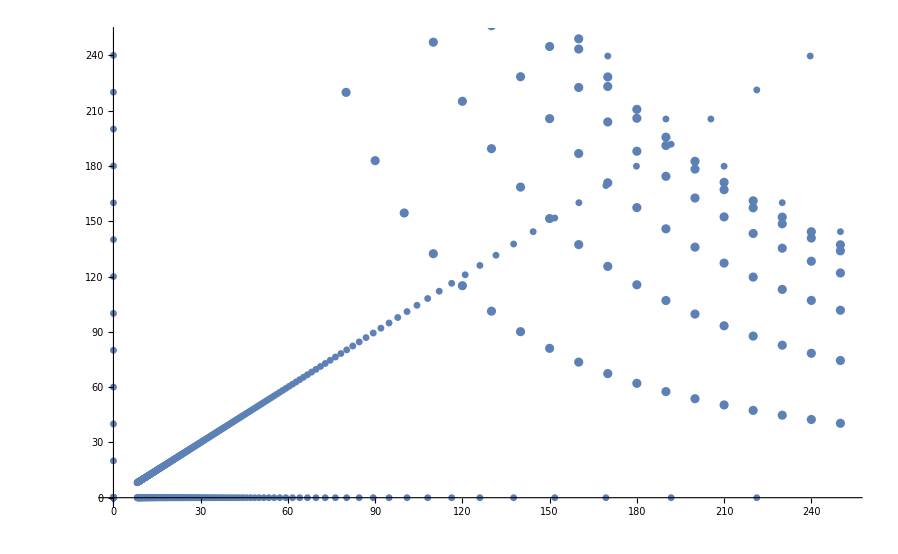

```mathematica
With[{b1=7,b2=7},Show[{ListPlot[kappa10[[b1;;b2]]],ListPlot[kappa300[[b1;;b2]]],ListPlot[kappa760[[b1;;b2]]],ListPlot[kappa1000[[b1;;b2]]],ListPlot[kappa1500[[b1;;b2]]],ListPlot[kappa2500[[b1;;b2]]],ListPlot[kappa3800[[b1;;b2]]]}]]
```

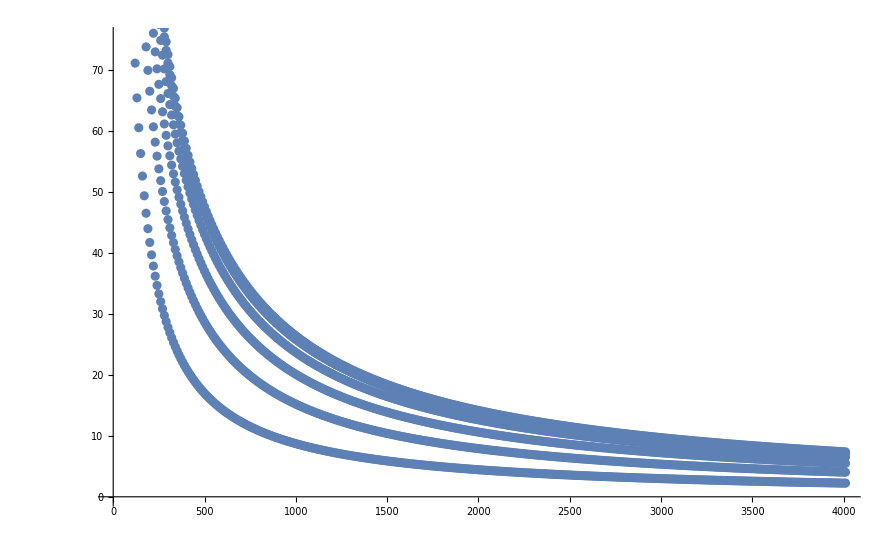

```mathematica
With[{b1=5,b2=5},Show[{ListPlot[kappa10[[b1;;b2]]],ListPlot[kappa300[[b1;;b2]]],ListPlot[kappa760[[b1;;b2]]],ListPlot[kappa1000[[b1;;b2]]],ListPlot[kappa1500[[b1;;b2]]],ListPlot[kappa2500[[b1;;b2]]],ListPlot[kappa3800[[b1;;b2]]]}]]
```

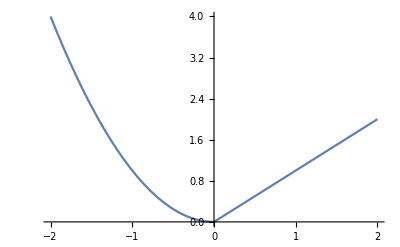

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

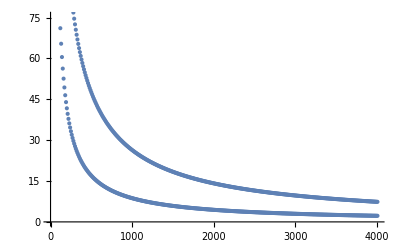

```mathematica
Show[{ListPlot@kappa10[[5]],ListPlot@kappa3800[[5]]}]
```

```mathematica
Transpose[kappa10[[1]]][[2]][[1]]
```

0.0124921953791471072

```mathematica
kappa10[[1]]//Length
```

401

```mathematica
tList={1,10,300,760,1000,1500,2500,3800};

tList2={1,3800};
tList3=tList/10
(*nameList={"kappa0","kappa10","kappa300","kappa760","kappa1000","kappa1500","kappa2500","kappa3800"};*)
nameList={kappa0,kappa10,kappa300,kappa760,kappa1000,kappa1500,kappa2500,kappa3800};
```

{1/10,1,30,76,100,150,250,380}

```mathematica
nameList//Length
nameList[[1]][[1]]//Length
nameList[[2]][[1]]//Length
nameList[[3]][[1]]//Length
nameList[[4]][[1]]//Length
nameList[[5]][[1]]//Length
nameList[[6]][[1]]//Length
nameList[[7]][[1]]//Length
```

8

1404

401

401

401

«3 more identical outputs»

```mathematica
nameList[[5]][[1]]//Length
```

115

```mathematica
kappa760[[1]]//Length
```

401

```mathematica
Transpose[kappa10[[1]]][[2]][[10]]
```

5.75117320336817883

```mathematica
kappa[T_,size_]:=(1-(10*T-tList[[2]])/tList[[8]])*Transpose[kappa10[[size]]][[2]][[T]]+((10*T-tList[[2]])/tList[[8]])*Transpose[kappa3800[[size]]][[2]][[T]]
```

```mathematica
kappa2[T_,size_,T1_,T2_]:=(1-(10*T-tList[[T1]])/tList[[T2]])*Transpose[kappa10[[size]]][[2]][[T]]+((10*T-tList[[T1]])/tList[[T2]])*Transpose[kappa3800[[size]]][[2]][[T]]
```

```mathematica
kappa3[T_,size_,T1_,T2_]:=(1-(10*T-tList[[T1]])/tList[[T2]])*Transpose[Evaluate[nameList[[T1]]][[size]]][[2]][[T]]+((10*T-tList[[T1]])/tList[[T2]])*Transpose[Evaluate[nameList[[T2]]][[size]]][[2]][[T]]
(*T=temperature*)
(*size = {1..6 for 0.01bmf iso to BULK iso. 7 is bulk perf*)
(*T1= 10 300 760 1000 1500 2500*)
(*T2= 300 760 1000 1500 2500 3800*)
kappa4[T_,size_,T1_,T2_]:=(1-((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameList[[T1]]][[size]]][[2]][[T]]+(((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameList[[T2]]][[size]]][[2]][[T]]
```

```mathematica
(*old kappa10to3800bulk=Table[{T*10,kappa[T,7]},{T,1,380,1}];
kappa10to3800bulk2=Table[{T*10,kappa2[T,1,2,8]},{T,1,380,1}];*)
```

```mathematica
tList
```

{1,10,300,760,1000,1500,2500,3800}

```mathematica
tList[[2]]/10
```

1

```mathematica
tList[[2]]
tList[[3]]
```

10

300

```mathematica
kappa10to300bulk=Table[Join[Table[{T*10,kappa3[T,boundarySize,2,3]},{T,1,30}],Table[{T*10,kappa3[T,boundarySize,3,4]},{T,30,76}],Table[{T*10,kappa3[T,boundarySize,4,5]},{T,76,100}]],{boundarySize,1,1}];
```

```mathematica
kappa3[79,1,4,5]
```

9.14808457914609275

```mathematica
kappa300[[1]]//Length
kappa760[[1]]//Length
kappa1000[[1]]//Length
kappa1500[[1]]//Length
kappa2500[[1]]//Length
```

401

401

401

«2 more identical outputs»

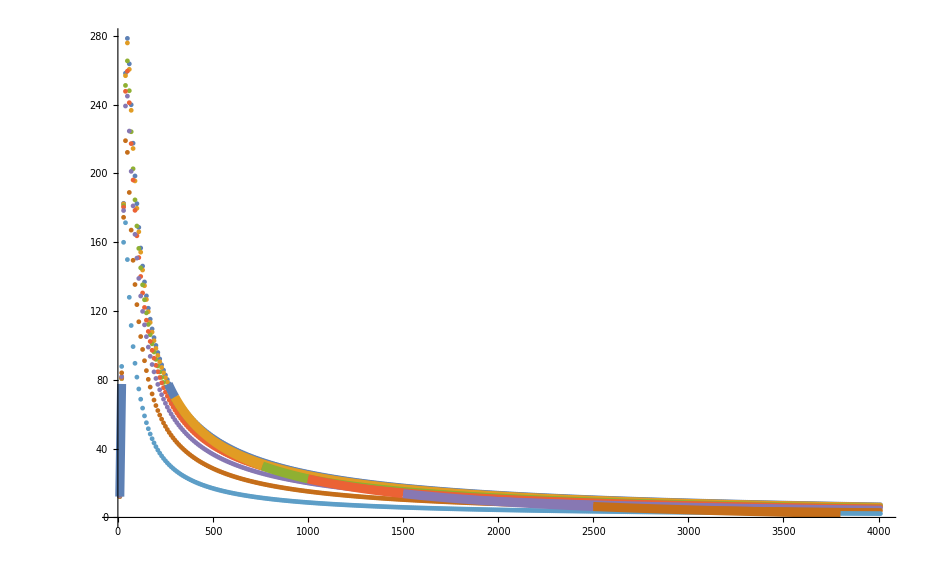

```mathematica
With[{size=4},Show[{ListPlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]],PlotRange->All],ListLinePlot[{Table[{T*10,kappa4[T,size,2,3]},{T,1,30}],Table[{T*10,kappa4[T,size,3,4]},{T,30,76}],Table[{T*10,kappa4[T,size,4,5]},{T,76,100}],Table[{T*10,kappa4[T,size,5,6]},{T,100,150}],Table[{T*10,kappa4[T,size,6,7]},{T,150,250}],Table[{T*10,kappa4[T,size,7,8]},{T,250,380}]},PlotStyle->Directive[Thickness[0.007]]]}]]
```

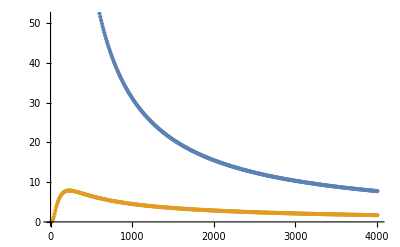

```mathematica
[[1::4]]
```

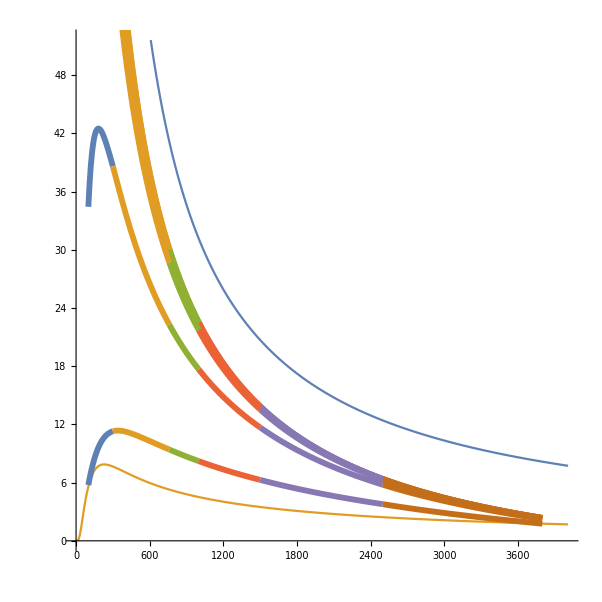

```mathematica
Show[{ListLinePlot[{kappa10[[7]],kappa3800[[1]]},AspectRatio->1],Table[With[{size=8-i},ListLinePlot[{Table[{T*10,kappa4[T,size,2,3]},{T,10,30}],Table[{T*10,kappa4[T,size,3,4]},{T,30,76}],Table[{T*10,kappa4[T,size,4,5]},{T,76,100}],Table[{T*10,kappa4[T,size,5,6]},{T,100,150}],Table[{T*10,kappa4[T,size,6,7]},{T,150,250}],Table[{T*10,kappa4[T,size,7,8]},{T,250,380}]},PlotStyle->Directive[Thickness[0.007]],PlotRange->{{50,3000},{0,200}}]],{i,2,7}]}]
```

```mathematica
tList3
```

tList3

```mathematica
Evaluate@tList3[[2]]
```

1

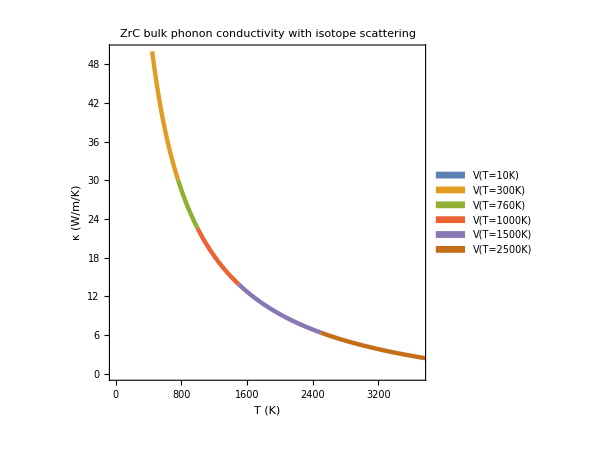

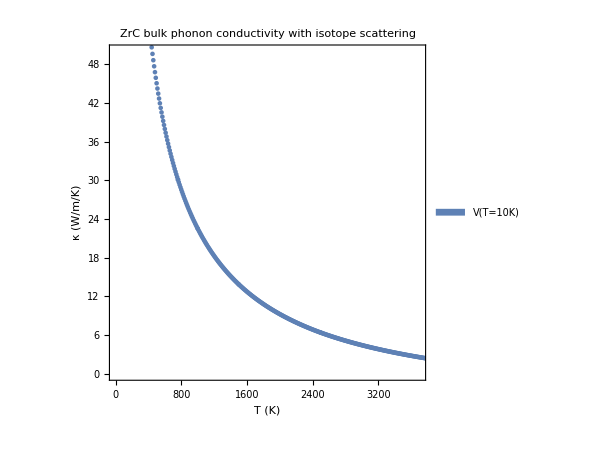

```mathematica
ListLinePlot[With[{size=6},Table[Table[{T*10,kappa4[T,size,i+1,i+2]},{T,Evaluate@tList3[[i+1]],Evaluate@tList3[[i+2]]}],{i,1,6}]],Evaluate@plotOptions]
ListPlot[With[{size=6},Join@@Table[Table[{T*10,kappa4[T,size,i+1,i+2]},{T,Evaluate@tList3[[i+1]],Evaluate@tList3[[i+2]]}],{i,1,6}]],Evaluate@plotOptions]
```

```mathematica
(*PlotLegends->Placed[SwatchLegend[{Style["1MBTE-LD - 0 K volume (NO ZP corrections)",15],Style["1MBTE-LD - MP volume",15]}],{0.53,0.87}]*)
plotOptions={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->Blackand,PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[{"V(T=10K)","V(T=300K)","V(T=760K)","V(T=1000K)","V(T=1500K)","V(T=2500K)","V(T=3800K)"}]};
p001=With[{size=1},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p01=With[{size=2},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p1=With[{size=3},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p10=With[{size=4},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p100=With[{size=5},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
```

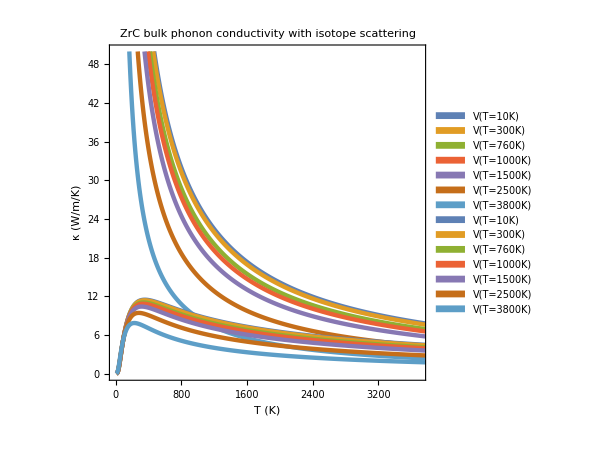

```mathematica
Show[p100,p001]
```

ListLinePlot::optx: Unknown option Framed→True in ListLinePlot[{{{10.,0.0124921953791471072},{20.,0.107701566224089579},{30.,0.385472210219584333},{40.,0.913708040900579777},«43»,{480.,11.1973285070877093},{490.,11.1583296300403276},{500.,11.1181736328460534},«351»},«6»},{Framed→True,«2»,PlotStyle→«9»[«1»]}].

Show::gcomb: Could not combine the graphics objects in Show[{,ListLinePlot[{{{10.,0.0124921953791471072},{20.,0.107701566224089579},{30.,0.385472210219584333},{40.,0.913708040900579777},«43»,{480.,11.1973285070877093},{490.,11.1583296300403276},{500.,11.1181736328460534},«351»},«5»,{{10.,«39»},«50»}},{«1»}]}].

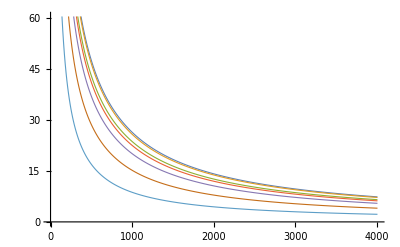
Show[{-Graphics-,ListLinePlot[{{{10.,0.0124921953791471072},{20.,0.107701566224089579},{30.,0.385472210219584333},{40.,0.913708040900579777},394,{3990.,4.33396484860165998},{4000.,4.32700752318353832},{4010.,4.32007460225406792}},5,{1}},{1}]}]
 |  |  |  |

```mathematica
p01=With[{size=2},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]]]];
p1=With[{size=3},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]]]];
p10=With[{size=4},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]]]];
p100=With[{size=5},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]]]];
pbulk=With[{size=6},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},PlotStyle->Directive[Thickness[0.002]]]];
Show[{p100,p001}]
```

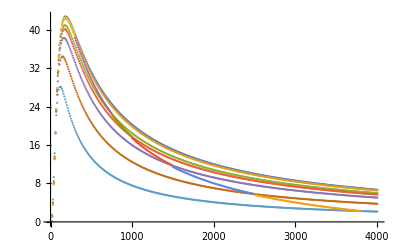

```mathematica
With[{size=2},ListPlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]],Table[{T*10,kappa3[T,2,2,3]},{T,1,29}],Table[{T*10,kappa3[T,2,2,4]},{T,30,75}],Table[{T*10,kappa3[T,2,2,5]},{T,76,99}],Table[{T*10,kappa3[T,2,2,6]},{T,100,149}],Table[{T*10,kappa3[T,2,2,7]},{T,150,249}],Table[{T*10,kappa3[T,2,2,8]},{T,251,380}]}]]
```

## Fix the t_kap for 0

```mathematica
kappa1000[[1]][[2]]
```

{20.,0.11101886172089305}

```mathematica
kappa10[[1]][[1]]
kappa300[[1]][[1]]
kappa760[[1]][[1]]
kappa1000[[1]][[1]]
kappa1500[[1]][[1]]
kappa2500[[1]][[1]]
kappa3800[[1]][[1]]
```

{10.,0.0124921953791471072}

{10.,0.0125249094711851593}

{10.,0.0127333237385209123}

{10.,0.012817562616960123}

{10.,0.0130716887472949721}

{10.,0.0139550324941971303}

{10.,0.016033670945726268}

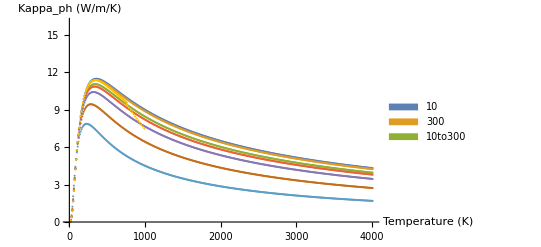

```mathematica
With[{size=1},ListPlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]],kappa10to300bulk[[size]]},AxesLabel->{"Temperature (K)","Kappa_ph (W/m/K)"},PlotLegends->SwatchLegend[{"10","300","10to300"}]]]
```

```mathematica
3
```

```mathematica
Table[{T*10,10/T},{T,1,9,1}]
```

{{10,10},{20,5},{30,10/3},{40,5/2},{50,2},{60,5/3},{70,10/7},{80,5/4},{90,10/9}}

```mathematica
Join[Table[{T*10,10/T},{T,1,9,1}],Table[{T*10,10/T},{T,10,19,1}]]
```

{{10,10},{20,5},{30,10/3},{40,5/2},{50,2},{60,5/3},{70,10/7},{80,5/4},{90,10/9},{100,1},{110,10/11},{120,5/6},{130,10/13},{140,5/7},{150,2/3},{160,5/8},{170,10/17},{180,5/9},{190,10/19}}